```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g1=Plot3D[PDF[MultinormalDistribution[{5,5},{{1,0.5},{0.5,1}}],{x,y}],{x,2,8},{y,2,8},PlotRange->Full, PerformanceGoal->"Quality",ViewPoint->{-1.7684998846522917,-2.4654940814308084,1.4979142473501272},ViewVertical->{0.,0.,1.},Boxed->False,AxesLabel->{"crime","unemployment","pdf"},Ticks->None,MeshStyle->{Black, Blue},PlotStyle->Automatic,PlotPoints->50,Mesh->{{4},{4.5}}]
```

-Graphics3D-

```mathematica
fRand[aXorY_]:=RandomVariate[NormalDistribution[5+0.5(aXorY-5),1-0.5^2],{1}][[1]]
fStep[aXInd_Integer,aX_,aY_]:=If[aXInd==1,{0,fRand[aY],aY},{1,aX,fRand[aX]}]
fGibbs[aNumIterations_Integer,aXStart_,aYStart_]:=NestList[fStep[#[[1]],#[[2]],#[[3]]]&,{1,aXStart,aYStart},aNumIterations][[All,2;;3]]
```

```mathematica
lNumSamples=fGibbs[100,5,5];
g3=SmoothHistogram3D[lNumSamples,ViewPoint->{-1.7684998846522917,-2.4654940814308084,1.4979142473501272},ViewVertical->{0.,0.,1.},Boxed->False,PlotRange->{{2,8},{2,8},Automatic},Mesh->None,AxesLabel->{"crime","unemployment","pdf"},Ticks->None,MeshStyle->{Black, Blue},PlotStyle->Automatic,PlotPoints->50,PlotLabel->"n = 100"]
```

-Graphics3D-

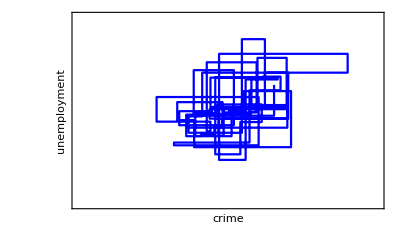

```mathematica
g2=ListLinePlot[lNumSamples,PlotRange->{{2,8},{2,8}},Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},FrameTicks->None,PlotStyle->Blue]
```

```mathematica
lNumSamples1=fGibbs[1000,5,5];
gFinal=Show[GraphicsGrid[{{g1,g2,g3},{,ListLinePlot[lNumSamples1,PlotRange->{{2,8},{2,8}},Frame->{True,True,False,False},FrameLabel->{"crime","unemployment"},FrameTicks->None,PlotStyle->Blue],SmoothHistogram3D[lNumSamples1,0.5,ViewPoint->{-1.7684998846522917,-2.4654940814308084,1.4979142473501272},ViewVertical->{0.,0.,1.},Boxed->False,PlotRange->{{2,8},{2,8},Automatic},Mesh->None,AxesLabel->{"crime","unemployment","pdf"},Ticks->None,MeshStyle->{Black, Blue},PlotStyle->Automatic,PlotPoints->50,PlotLabel->"n = 1000"]}}],ImageSize->800]
```

-Graphics-

```mathematica
Export["Gibbs_crimeMultivariateNormalSlice.png",gFinal]
```

Gibbs_crimeMultivariateNormalSlice.png